```mathematica
tab=Import["/Users/michelecastellana/Documents/finite_elements/biharmonic-equation/test_boundary_points.csv"];
tab=Table[{tab[[i,1]],tab[[i,2]]},{i,1,Length[tab]}]
```

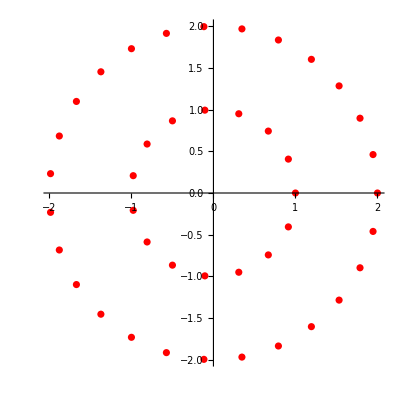

```mathematica
boundary=ListPlot[tab,AspectRatio->1,PlotStyle->Red]
```

```mathematica
tab=Import["/Users/michelecastellana/Documents/finite_elements/biharmonic-equation/test_bulk_points.csv"];
tab=Table[{tab[[i,1]],tab[[i,2]]},{i,1,Length[tab]}]
```

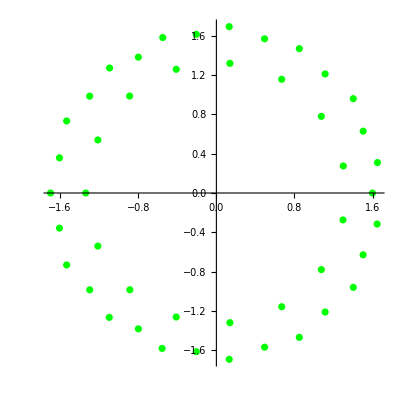

```mathematica
bulk=ListPlot[tab,AspectRatio->1,PlotStyle->Green]
```

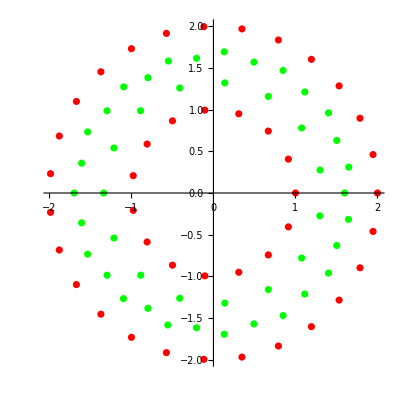

```mathematica
Show[boundary,bulk]
```